```mathematica
Map[{Re[#[[2]]]^2+Im[#[[2]]]^2==1}&,Select[Flatten[Table[ExpressionToList[N[Roots[(k/.x->x+1)==0,x]]],{k,Rest[DeleteDuplicates[Flatten[Table[FactorList[ChromaticPolynomial[CycleGraph[k],x]],{k,3,18}]]]]}]],Length[#]==2&]]
```

{{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True}}

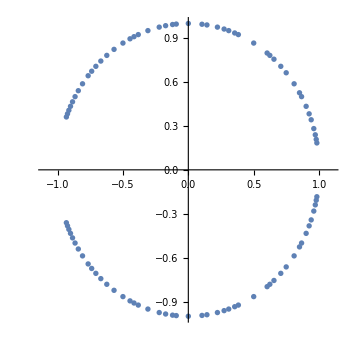

```mathematica
ListPlot[Map[{Re[#[[2]]],Im[#[[2]]]}&,Select[Flatten[Table[ExpressionToList[N[Roots[(k/.x->x+1)==0,x]]],{k,Rest[DeleteDuplicates[Flatten[Table[FactorList[ChromaticPolynomial[CycleGraph[k],x]],{k,3,18}]]]]}]],Length[#]==2&]],PlotRange->{{-1.1,1.1},All}, AspectRatio->1]
```

```mathematica
Map[Factor[(#/.x->x-1)]&,Rest[DeleteDuplicates[Flatten[Table[FactorList[ChromaticPolynomial[CycleGraph[k],x]],{k,3,18}]]]]]//TableForm
```

-3+x
-2+x
-1+x
7-5 x+x^2
5-4 x+x^2
31-49 x+31 x^2-9 x^3+x^4
3-3 x+x^2
127-321 x+351 x^2-209 x^3+71 x^4-13 x^5+x^6
17-32 x+24 x^2-8 x^3+x^4
73-204 x+246 x^2-161 x^3+60 x^4-12 x^5+x^6
11-23 x+19 x^2-7 x^3+x^4
2047-9217 x+18943 x^2-23297 x^3+18943 x^4-10625 x^5+4159 x^6-1121 x^7+199 x^8-21 x^9+x^10
13-28 x+23 x^2-8 x^3+x^4
8191-45057 x+114687 x^2-178177 x^3+187903 x^4-141569 x^5+78079 x^6-31745 x^7+9439 x^8-2001 x^9+287 x^10-25 x^11+x^12
43-135 x+179 x^2-127 x^3+51 x^4-11 x^5+x^6
151-635 x+1182 x^2-1265 x^3+849 x^4-365 x^5+98 x^6-15 x^7+x^8
257-1024 x+1792 x^2-1792 x^3+1120 x^4-448 x^5+112 x^6-16 x^7+x^8
131071-983041 x+3473407 x^2-7667713 x^3+11829247 x^4-13516801 x^5+11829247 x^6-8085505 x^7+4361215 x^8-1862145 x^9+627199 x^10-164865 x^11+33151 x^12-4929 x^13+511 x^14-33 x^15+x^16

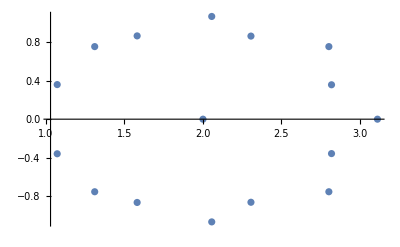

```mathematica
Map[{Re[#],Im[#]}&,Map[Last[Last[#]]&,NSolve[257-1024 x+1792 x^2-1792 x^3+1120 x^4-448 x^5+112 x^6-16 x^7+x^8==131071-983041 x+3473407 x^2-7667713 x^3+11829247 x^4-13516801 x^5+11829247 x^6-8085505 x^7+4361215 x^8-1862145 x^9+627199 x^10-164865 x^11+33151 x^12-4929 x^13+511 x^14-33 x^15+x^16,x]]]//ListPlot
```

```mathematica
Solve[2047-9217 x+18943 x^2-23297 x^3+18943 x^4-10625 x^5+4159 x^6-1121 x^7+199 x^8-21 x^9+x^10==8191-45057 x+114687 x^2-178177 x^3+187903 x^4-141569 x^5+78079 x^6-31745 x^7+9439 x^8-2001 x^9+287 x^10-25 x^11+x^12,x]
```

```mathematica
N[Roots[0==73-204 x+246 x^2-161 x^3+60 x^4-12 x^5+x^6,x]]//ToRules
```

Sequence[{x→2.93969-0.34202 ⅈ},{x→1.82635+0.984808 ⅈ},{x→1.23396-0.642788 ⅈ},{x→2.93969+0.34202 ⅈ},{x→1.23396+0.642788 ⅈ},{x→1.82635-0.984808 ⅈ}]

```mathematica
Select[Flatten[Table[ExpressionToList[N[Roots[k==0,x]]],{k,Rest[DeleteDuplicates[Flatten[Table[FactorList[ChromaticPolynomial[CycleGraph[k],x]],{k,3,18}]]]]}]],Length[#]==2&]
```

{x==1.5-0.866025 ⅈ,x==1.5+0.866025 ⅈ,x==1.-1. ⅈ,x==1.+1. ⅈ,x==1.80902-0.587785 ⅈ,x==1.80902+0.587785 ⅈ,x==0.690983-0.951057 ⅈ,x==0.690983+0.951057 ⅈ,x==0.5+0.866025 ⅈ,x==0.5-0.866025 ⅈ,x==0.37651-0.781831 ⅈ,x==0.37651+0.781831 ⅈ,x==1.22252-0.974928 ⅈ,x==1.22252+0.974928 ⅈ,x==1.90097-0.433884 ⅈ,x==1.90097+0.433884 ⅈ,x==1.70711-0.707107 ⅈ,x==0.292893+0.707107 ⅈ,x==0.292893-0.707107 ⅈ,x==1.70711+0.707107 ⅈ,x==1.93969-0.34202 ⅈ,x==0.826352+0.984808 ⅈ,x==0.233956-0.642788 ⅈ,x==1.93969+0.34202 ⅈ,x==0.233956+0.642788 ⅈ,x==0.826352-0.984808 ⅈ,x==0.190983-0.587785 ⅈ,x==0.190983+0.587785 ⅈ,x==1.30902-0.951057 ⅈ,x==1.30902+0.951057 ⅈ,x==0.158746-0.540641 ⅈ,x==0.158746+0.540641 ⅈ,x==0.584585-0.909632 ⅈ,x==0.584585+0.909632 ⅈ,x==1.14231-0.989821 ⅈ,x==1.14231+0.989821 ⅈ,x==1.65486-0.75575 ⅈ,x==1.65486+0.75575 ⅈ,x==1.95949-0.281733 ⅈ,x==1.95949+0.281733 ⅈ,x==0.133975+0.5 ⅈ,x==1.86603-0.5 ⅈ,x==0.133975-0.5 ⅈ,x==1.86603+0.5 ⅈ,x==0.114544-0.464723 ⅈ,x==0.114544+0.464723 ⅈ,x==0.431935-0.822984 ⅈ,x==0.431935+0.822984 ⅈ,x==0.879463-0.992709 ⅈ,x==0.879463+0.992709 ⅈ,x==1.3546-0.935016 ⅈ,x==1.3546+0.935016 ⅈ,x==1.74851-0.663123 ⅈ,x==1.74851+0.663123 ⅈ,x==1.97094-0.239316 ⅈ,x==1.97094+0.239316 ⅈ,x==0.0990311-0.433884 ⅈ,x==0.0990311+0.433884 ⅈ,x==0.777479-0.974928 ⅈ,x==0.777479+0.974928 ⅈ,x==1.62349-0.781831 ⅈ,x==1.62349+0.781831 ⅈ,x==0.0864545-0.406737 ⅈ,x==0.0864545+0.406737 ⅈ,x==0.330869-0.743145 ⅈ,x==0.330869+0.743145 ⅈ,x==1.10453-0.994522 ⅈ,x==1.10453+0.994522 ⅈ,x==1.97815-0.207912 ⅈ,x==1.97815+0.207912 ⅈ,x==1.38268-0.92388 ⅈ,x==0.617317+0.92388 ⅈ,x==0.0761205-0.382683 ⅈ,x==1.92388+0.382683 ⅈ,x==1.92388-0.382683 ⅈ,x==0.0761205+0.382683 ⅈ,x==0.617317-0.92388 ⅈ,x==1.38268+0.92388 ⅈ,x==0.0675278-0.361242 ⅈ,x==0.0675278+0.361242 ⅈ,x==0.260991-0.673696 ⅈ,x==0.260991+0.673696 ⅈ,x==0.554262-0.895163 ⅈ,x==0.554262+0.895163 ⅈ,x==0.907732-0.995734 ⅈ,x==0.907732+0.995734 ⅈ,x==1.27366-0.961826 ⅈ,x==1.27366+0.961826 ⅈ,x==1.60263-0.798017 ⅈ,x==1.60263+0.798017 ⅈ,x==1.85022-0.526432 ⅈ,x==1.85022+0.526432 ⅈ,x==1.98297-0.18375 ⅈ,x==1.98297+0.18375 ⅈ}

```mathematica
equations=Map[Factor[(#/.x->x-1)]&,Rest[DeleteDuplicates[Flatten[Table[FactorList[ChromaticPolynomial[CycleGraph[k],x]],{k,3,18}]]]]];
```

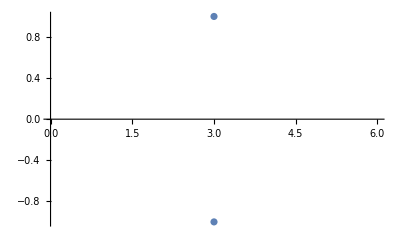
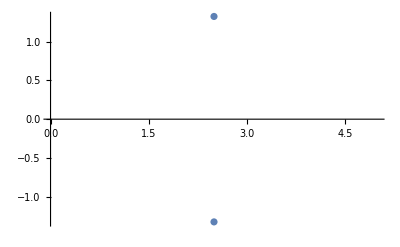
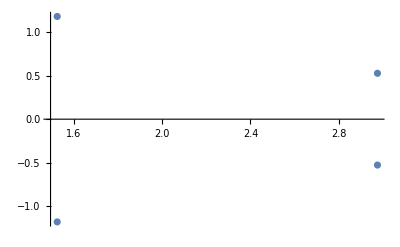
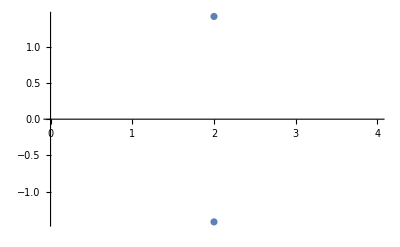
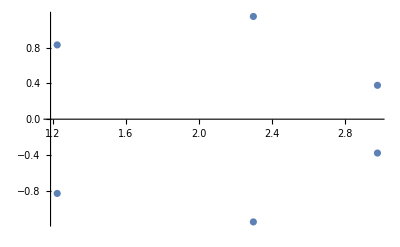
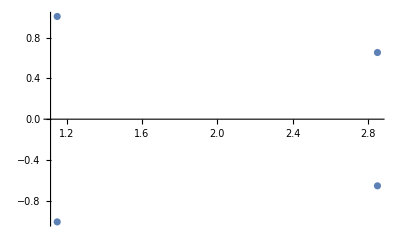
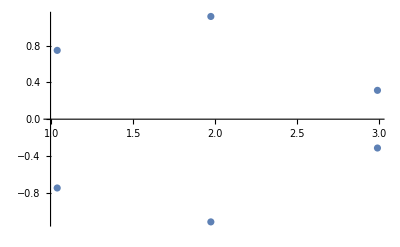
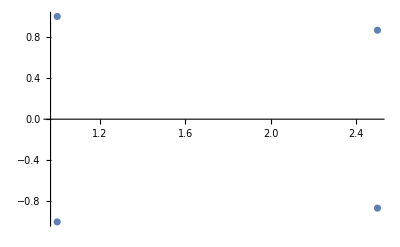
-Graphics--2+x
-3+x | -Graphics--1+x
-3+x | -Graphics-7-5 x+x^2
-3+x | -Graphics-5-4 x+x^2
-3+x | -Graphics-31-49 x+31 x^2-9 x^3+x^4
-3+x | -Graphics-3-3 x+x^2
-3+x | -Graphics-127-321 x+351 x^2-209 x^3+71 x^4-13 x^5+x^6
-3+x | -Graphics-17-32 x+24 x^2-8 x^3+x^4
-3+x | -Graphics-73-204 x+246 x^2-161 x^3+60 x^4-12 x^5+x^6
-3+x | -Graphics-11-23 x+19 x^2-7 x^3+x^4
-3+x | -Graphics-2047-9217 x+18943 x^2-23297 x^3+18943 x^4-10625 x^5+4159 x^6-1121 x^7+199 x^8-21 x^9+x^10
-3+x | -Graphics-13-28 x+23 x^2-8 x^3+x^4
-3+x | -Graphics-8191-45057 x+114687 x^2-178177 x^3+187903 x^4-141569 x^5+78079 x^6-31745 x^7+9439 x^8-2001 x^9+287 x^10-25 x^11+x^12
-3+x | -Graphics-43-135 x+179 x^2-127 x^3+51 x^4-11 x^5+x^6
-3+x | -Graphics-151-635 x+1182 x^2-1265 x^3+849 x^4-365 x^5+98 x^6-15 x^7+x^8
-3+x | -Graphics-257-1024 x+1792 x^2-1792 x^3+1120 x^4-448 x^5+112 x^6-16 x^7+x^8
-3+x | -Graphics-131071-983041 x+3473407 x^2-7667713 x^3+11829247 x^4-13516801 x^5+11829247 x^6-8085505 x^7+4361215 x^8-1862145 x^9+627199 x^10-164865 x^11+33151 x^12-4929 x^13+511 x^14-33 x^15+x^16
-3+x
-Graphics--1+x
-2+x | -Graphics-7-5 x+x^2
-2+x | -Graphics-5-4 x+x^2
-2+x | -Graphics-31-49 x+31 x^2-9 x^3+x^4
-2+x | -Graphics-3-3 x+x^2
-2+x | -Graphics-127-321 x+351 x^2-209 x^3+71 x^4-13 x^5+x^6
-2+x | -Graphics-17-32 x+24 x^2-8 x^3+x^4
-2+x | -Graphics-73-204 x+246 x^2-161 x^3+60 x^4-12 x^5+x^6
-2+x | -Graphics-11-23 x+19 x^2-7 x^3+x^4
-2+x | -Graphics-2047-9217 x+18943 x^2-23297 x^3+18943 x^4-10625 x^5+4159 x^6-1121 x^7+199 x^8-21 x^9+x^10
-2+x | -Graphics-13-28 x+23 x^2-8 x^3+x^4
-2+x | -Graphics-8191-45057 x+114687 x^2-178177 x^3+187903 x^4-141569 x^5+78079 x^6-31745 x^7+9439 x^8-2001 x^9+287 x^10-25 x^11+x^12
-2+x | -Graphics-43-135 x+179 x^2-127 x^3+51 x^4-11 x^5+x^6
-2+x | -Graphics-151-635 x+1182 x^2-1265 x^3+849 x^4-365 x^5+98 x^6-15 x^7+x^8
-2+x | -Graphics-257-1024 x+1792 x^2-1792 x^3+1120 x^4-448 x^5+112 x^6-16 x^7+x^8
-2+x | -Graphics-131071-983041 x+3473407 x^2-7667713 x^3+11829247 x^4-13516801 x^5+11829247 x^6-8085505 x^7+4361215 x^8-1862145 x^9+627199 x^10-164865 x^11+33151 x^12-4929 x^13+511 x^14-33 x^15+x^16
-2+x | 
-Graphics-7-5 x+x^2
-1+x | -Graphics-5-4 x+x^2
-1+x | -Graphics-31-49 x+31 x^2-9 x^3+x^4
-1+x | -Graphics-3-3 x+x^2
-1+x | -Graphics-127-321 x+351 x^2-209 x^3+71 x^4-13 x^5+x^6
-1+x | -Graphics-17-32 x+24 x^2-8 x^3+x^4
-1+x | -Graphics-73-204 x+246 x^2-161 x^3+60 x^4-12 x^5+x^6
-1+x | -Graphics-11-23 x+19 x^2-7 x^3+x^4
-1+x | -Graphics-2047-9217 x+18943 x^2-23297 x^3+18943 x^4-10625 x^5+4159 x^6-1121 x^7+199 x^8-21 x^9+x^10
-1+x | -Graphics-13-28 x+23 x^2-8 x^3+x^4
-1+x | -Graphics-8191-45057 x+114687 x^2-178177 x^3+187903 x^4-141569 x^5+78079 x^6-31745 x^7+9439 x^8-2001 x^9+287 x^10-25 x^11+x^12
-1+x | -Graphics-43-135 x+179 x^2-127 x^3+51 x^4-11 x^5+x^6
-1+x | -Graphics-151-635 x+1182 x^2-1265 x^3+849 x^4-365 x^5+98 x^6-15 x^7+x^8
-1+x | -Graphics-257-1024 x+1792 x^2-1792 x^3+1120 x^4-448 x^5+112 x^6-16 x^7+x^8
-1+x | -Graphics-131071-983041 x+3473407 x^2-7667713 x^3+11829247 x^4-13516801 x^5+11829247 x^6-8085505 x^7+4361215 x^8-1862145 x^9+627199 x^10-164865 x^11+33151 x^12-4929 x^13+511 x^14-33 x^15+x^16
-1+x |  | 
-Graphics-5-4 x+x^2
7-5 x+x^2 | -Graphics-31-49 x+31 x^2-9 x^3+x^4
7-5 x+x^2 | -Graphics-3-3 x+x^2
7-5 x+x^2 | -Graphics-127-321 x+351 x^2-209 x^3+71 x^4-13 x^5+x^6
7-5 x+x^2 | -Graphics-17-32 x+24 x^2-8 x^3+x^4
7-5 x+x^2 | -Graphics-73-204 x+246 x^2-161 x^3+60 x^4-12 x^5+x^6
7-5 x+x^2 | -Graphics-11-23 x+19 x^2-7 x^3+x^4
7-5 x+x^2 | -Graphics-2047-9217 x+18943 x^2-23297 x^3+18943 x^4-10625 x^5+4159 x^6-1121 x^7+199 x^8-21 x^9+x^10
7-5 x+x^2 | -Graphics-13-28 x+23 x^2-8 x^3+x^4
7-5 x+x^2 | -Graphics-8191-45057 x+114687 x^2-178177 x^3+187903 x^4-141569 x^5+78079 x^6-31745 x^7+9439 x^8-2001 x^9+287 x^10-25 x^11+x^12
7-5 x+x^2 | -Graphics-43-135 x+179 x^2-127 x^3+51 x^4-11 x^5+x^6
7-5 x+x^2 | -Graphics-151-635 x+1182 x^2-1265 x^3+849 x^4-365 x^5+98 x^6-15 x^7+x^8
7-5 x+x^2 | -Graphics-257-1024 x+1792 x^2-1792 x^3+1120 x^4-448 x^5+112 x^6-16 x^7+x^8
7-5 x+x^2 | -Graphics-131071-983041 x+3473407 x^2-7667713 x^3+11829247 x^4-13516801 x^5+11829247 x^6-8085505 x^7+4361215 x^8-1862145 x^9+627199 x^10-164865 x^11+33151 x^12-4929 x^13+511 x^14-33 x^15+x^16
7-5 x+x^2 |  |  | 
-Graphics-31-49 x+31 x^2-9 x^3+x^4
5-4 x+x^2 | -Graphics-3-3 x+x^2
5-4 x+x^2 | -Graphics-127-321 x+351 x^2-209 x^3+71 x^4-13 x^5+x^6
5-4 x+x^2 | -Graphics-17-32 x+24 x^2-8 x^3+x^4
5-4 x+x^2 | -Graphics-73-204 x+246 x^2-161 x^3+60 x^4-12 x^5+x^6
5-4 x+x^2 | -Graphics-11-23 x+19 x^2-7 x^3+x^4
5-4 x+x^2 | -Graphics-2047-9217 x+18943 x^2-23297 x^3+18943 x^4-10625 x^5+4159 x^6-1121 x^7+199 x^8-21 x^9+x^10
5-4 x+x^2 | -Graphics-13-28 x+23 x^2-8 x^3+x^4
5-4 x+x^2 | -Graphics-8191-45057 x+114687 x^2-178177 x^3+187903 x^4-141569 x^5+78079 x^6-31745 x^7+9439 x^8-2001 x^9+287 x^10-25 x^11+x^12
5-4 x+x^2 | -Graphics-43-135 x+179 x^2-127 x^3+51 x^4-11 x^5+x^6
5-4 x+x^2 | -Graphics-151-635 x+1182 x^2-1265 x^3+849 x^4-365 x^5+98 x^6-15 x^7+x^8
5-4 x+x^2 | -Graphics-257-1024 x+1792 x^2-1792 x^3+1120 x^4-448 x^5+112 x^6-16 x^7+x^8
5-4 x+x^2 | -Graphics-131071-983041 x+3473407 x^2-7667713 x^3+11829247 x^4-13516801 x^5+11829247 x^6-8085505 x^7+4361215 x^8-1862145 x^9+627199 x^10-164865 x^11+33151 x^12-4929 x^13+511 x^14-33 x^15+x^16
5-4 x+x^2 |  |  |  | 
-Graphics-3-3 x+x^2
31-49 x+31 x^2-9 x^3+x^4 | -Graphics-127-321 x+351 x^2-209 x^3+71 x^4-13 x^5+x^6
31-49 x+31 x^2-9 x^3+x^4 | -Graphics-17-32 x+24 x^2-8 x^3+x^4
31-49 x+31 x^2-9 x^3+x^4 | -Graphics-73-204 x+246 x^2-161 x^3+60 x^4-12 x^5+x^6
31-49 x+31 x^2-9 x^3+x^4 | -Graphics-11-23 x+19 x^2-7 x^3+x^4
31-49 x+31 x^2-9 x^3+x^4 | -Graphics-2047-9217 x+18943 x^2-23297 x^3+18943 x^4-10625 x^5+4159 x^6-1121 x^7+199 x^8-21 x^9+x^10
31-49 x+31 x^2-9 x^3+x^4 | -Graphics-13-28 x+23 x^2-8 x^3+x^4
31-49 x+31 x^2-9 x^3+x^4 | -Graphics-8191-45057 x+114687 x^2-178177 x^3+187903 x^4-141569 x^5+78079 x^6-31745 x^7+9439 x^8-2001 x^9+287 x^10-25 x^11+x^12
31-49 x+31 x^2-9 x^3+x^4 | -Graphics-43-135 x+179 x^2-127 x^3+51 x^4-11 x^5+x^6
31-49 x+31 x^2-9 x^3+x^4 | -Graphics-151-635 x+1182 x^2-1265 x^3+849 x^4-365 x^5+98 x^6-15 x^7+x^8
31-49 x+31 x^2-9 x^3+x^4 | -Graphics-257-1024 x+1792 x^2-1792 x^3+1120 x^4-448 x^5+112 x^6-16 x^7+x^8
31-49 x+31 x^2-9 x^3+x^4 | -Graphics-131071-983041 x+3473407 x^2-7667713 x^3+11829247 x^4-13516801 x^5+11829247 x^6-8085505 x^7+4361215 x^8-1862145 x^9+627199 x^10-164865 x^11+33151 x^12-4929 x^13+511 x^14-33 x^15+x^16
31-49 x+31 x^2-9 x^3+x^4 |  |  |  |  | 
-Graphics-127-321 x+351 x^2-209 x^3+71 x^4-13 x^5+x^6
3-3 x+x^2 | -Graphics-17-32 x+24 x^2-8 x^3+x^4
3-3 x+x^2 | -Graphics-73-204 x+246 x^2-161 x^3+60 x^4-12 x^5+x^6
3-3 x+x^2 | -Graphics-11-23 x+19 x^2-7 x^3+x^4
3-3 x+x^2 | -Graphics-2047-9217 x+18943 x^2-23297 x^3+18943 x^4-10625 x^5+4159 x^6-1121 x^7+199 x^8-21 x^9+x^10
3-3 x+x^2 | -Graphics-13-28 x+23 x^2-8 x^3+x^4
3-3 x+x^2 | -Graphics-8191-45057 x+114687 x^2-178177 x^3+187903 x^4-141569 x^5+78079 x^6-31745 x^7+9439 x^8-2001 x^9+287 x^10-25 x^11+x^12
3-3 x+x^2 | -Graphics-43-135 x+179 x^2-127 x^3+51 x^4-11 x^5+x^6
3-3 x+x^2 | -Graphics-151-635 x+1182 x^2-1265 x^3+849 x^4-365 x^5+98 x^6-15 x^7+x^8
3-3 x+x^2 | -Graphics-257-1024 x+1792 x^2-1792 x^3+1120 x^4-448 x^5+112 x^6-16 x^7+x^8
3-3 x+x^2 | -Graphics-131071-983041 x+3473407 x^2-7667713 x^3+11829247 x^4-13516801 x^5+11829247 x^6-8085505 x^7+4361215 x^8-1862145 x^9+627199 x^10-164865 x^11+33151 x^12-4929 x^13+511 x^14-33 x^15+x^16
3-3 x+x^2 |  |  |  |  |  | 
-Graphics-17-32 x+24 x^2-8 x^3+x^4
127-321 x+351 x^2-209 x^3+71 x^4-13 x^5+x^6 | -Graphics-73-204 x+246 x^2-161 x^3+60 x^4-12 x^5+x^6
127-321 x+351 x^2-209 x^3+71 x^4-13 x^5+x^6 | -Graphics-11-23 x+19 x^2-7 x^3+x^4
127-321 x+351 x^2-209 x^3+71 x^4-13 x^5+x^6 | -Graphics-2047-9217 x+18943 x^2-23297 x^3+18943 x^4-10625 x^5+4159 x^6-1121 x^7+199 x^8-21 x^9+x^10
127-321 x+351 x^2-209 x^3+71 x^4-13 x^5+x^6 | -Graphics-13-28 x+23 x^2-8 x^3+x^4
127-321 x+351 x^2-209 x^3+71 x^4-13 x^5+x^6 | -Graphics-8191-45057 x+114687 x^2-178177 x^3+187903 x^4-141569 x^5+78079 x^6-31745 x^7+9439 x^8-2001 x^9+287 x^10-25 x^11+x^12
127-321 x+351 x^2-209 x^3+71 x^4-13 x^5+x^6 | -Graphics-43-135 x+179 x^2-127 x^3+51 x^4-11 x^5+x^6
127-321 x+351 x^2-209 x^3+71 x^4-13 x^5+x^6 | -Graphics-151-635 x+1182 x^2-1265 x^3+849 x^4-365 x^5+98 x^6-15 x^7+x^8
127-321 x+351 x^2-209 x^3+71 x^4-13 x^5+x^6 | -Graphics-257-1024 x+1792 x^2-1792 x^3+1120 x^4-448 x^5+112 x^6-16 x^7+x^8
127-321 x+351 x^2-209 x^3+71 x^4-13 x^5+x^6 | -Graphics-131071-983041 x+3473407 x^2-7667713 x^3+11829247 x^4-13516801 x^5+11829247 x^6-8085505 x^7+4361215 x^8-1862145 x^9+627199 x^10-164865 x^11+33151 x^12-4929 x^13+511 x^14-33 x^15+x^16
127-321 x+351 x^2-209 x^3+71 x^4-13 x^5+x^6 |  |  |  |  |  |  | 
-Graphics-73-204 x+246 x^2-161 x^3+60 x^4-12 x^5+x^6
17-32 x+24 x^2-8 x^3+x^4 | -Graphics-11-23 x+19 x^2-7 x^3+x^4
17-32 x+24 x^2-8 x^3+x^4 | -Graphics-2047-9217 x+18943 x^2-23297 x^3+18943 x^4-10625 x^5+4159 x^6-1121 x^7+199 x^8-21 x^9+x^10
17-32 x+24 x^2-8 x^3+x^4 | -Graphics-13-28 x+23 x^2-8 x^3+x^4
17-32 x+24 x^2-8 x^3+x^4 | -Graphics-8191-45057 x+114687 x^2-178177 x^3+187903 x^4-141569 x^5+78079 x^6-31745 x^7+9439 x^8-2001 x^9+287 x^10-25 x^11+x^12
17-32 x+24 x^2-8 x^3+x^4 | -Graphics-43-135 x+179 x^2-127 x^3+51 x^4-11 x^5+x^6
17-32 x+24 x^2-8 x^3+x^4 | -Graphics-151-635 x+1182 x^2-1265 x^3+849 x^4-365 x^5+98 x^6-15 x^7+x^8
17-32 x+24 x^2-8 x^3+x^4 | -Graphics-257-1024 x+1792 x^2-1792 x^3+1120 x^4-448 x^5+112 x^6-16 x^7+x^8
17-32 x+24 x^2-8 x^3+x^4 | -Graphics-131071-983041 x+3473407 x^2-7667713 x^3+11829247 x^4-13516801 x^5+11829247 x^6-8085505 x^7+4361215 x^8-1862145 x^9+627199 x^10-164865 x^11+33151 x^12-4929 x^13+511 x^14-33 x^15+x^16
17-32 x+24 x^2-8 x^3+x^4 |  |  |  |  |  |  |  | 
-Graphics-11-23 x+19 x^2-7 x^3+x^4
73-204 x+246 x^2-161 x^3+60 x^4-12 x^5+x^6 | -Graphics-2047-9217 x+18943 x^2-23297 x^3+18943 x^4-10625 x^5+4159 x^6-1121 x^7+199 x^8-21 x^9+x^10
73-204 x+246 x^2-161 x^3+60 x^4-12 x^5+x^6 | -Graphics-13-28 x+23 x^2-8 x^3+x^4
73-204 x+246 x^2-161 x^3+60 x^4-12 x^5+x^6 | -Graphics-8191-45057 x+114687 x^2-178177 x^3+187903 x^4-141569 x^5+78079 x^6-31745 x^7+9439 x^8-2001 x^9+287 x^10-25 x^11+x^12
73-204 x+246 x^2-161 x^3+60 x^4-12 x^5+x^6 | -Graphics-43-135 x+179 x^2-127 x^3+51 x^4-11 x^5+x^6
73-204 x+246 x^2-161 x^3+60 x^4-12 x^5+x^6 | -Graphics-151-635 x+1182 x^2-1265 x^3+849 x^4-365 x^5+98 x^6-15 x^7+x^8
73-204 x+246 x^2-161 x^3+60 x^4-12 x^5+x^6 | -Graphics-257-1024 x+1792 x^2-1792 x^3+1120 x^4-448 x^5+112 x^6-16 x^7+x^8
73-204 x+246 x^2-161 x^3+60 x^4-12 x^5+x^6 | -Graphics-131071-983041 x+3473407 x^2-7667713 x^3+11829247 x^4-13516801 x^5+11829247 x^6-8085505 x^7+4361215 x^8-1862145 x^9+627199 x^10-164865 x^11+33151 x^12-4929 x^13+511 x^14-33 x^15+x^16
73-204 x+246 x^2-161 x^3+60 x^4-12 x^5+x^6 |  |  |  |  |  |  |  |  | 
-Graphics-2047-9217 x+18943 x^2-23297 x^3+18943 x^4-10625 x^5+4159 x^6-1121 x^7+199 x^8-21 x^9+x^10
11-23 x+19 x^2-7 x^3+x^4 | -Graphics-13-28 x+23 x^2-8 x^3+x^4
11-23 x+19 x^2-7 x^3+x^4 | -Graphics-8191-45057 x+114687 x^2-178177 x^3+187903 x^4-141569 x^5+78079 x^6-31745 x^7+9439 x^8-2001 x^9+287 x^10-25 x^11+x^12
11-23 x+19 x^2-7 x^3+x^4 | -Graphics-43-135 x+179 x^2-127 x^3+51 x^4-11 x^5+x^6
11-23 x+19 x^2-7 x^3+x^4 | -Graphics-151-635 x+1182 x^2-1265 x^3+849 x^4-365 x^5+98 x^6-15 x^7+x^8
11-23 x+19 x^2-7 x^3+x^4 | -Graphics-257-1024 x+1792 x^2-1792 x^3+1120 x^4-448 x^5+112 x^6-16 x^7+x^8
11-23 x+19 x^2-7 x^3+x^4 | -Graphics-131071-983041 x+3473407 x^2-7667713 x^3+11829247 x^4-13516801 x^5+11829247 x^6-8085505 x^7+4361215 x^8-1862145 x^9+627199 x^10-164865 x^11+33151 x^12-4929 x^13+511 x^14-33 x^15+x^16
11-23 x+19 x^2-7 x^3+x^4 |  |  |  |  |  |  |  |  |  | 
-Graphics-13-28 x+23 x^2-8 x^3+x^4
2047-9217 x+18943 x^2-23297 x^3+18943 x^4-10625 x^5+4159 x^6-1121 x^7+199 x^8-21 x^9+x^10 | -Graphics-8191-45057 x+114687 x^2-178177 x^3+187903 x^4-141569 x^5+78079 x^6-31745 x^7+9439 x^8-2001 x^9+287 x^10-25 x^11+x^12
2047-9217 x+18943 x^2-23297 x^3+18943 x^4-10625 x^5+4159 x^6-1121 x^7+199 x^8-21 x^9+x^10 | -Graphics-43-135 x+179 x^2-127 x^3+51 x^4-11 x^5+x^6
2047-9217 x+18943 x^2-23297 x^3+18943 x^4-10625 x^5+4159 x^6-1121 x^7+199 x^8-21 x^9+x^10 | -Graphics-151-635 x+1182 x^2-1265 x^3+849 x^4-365 x^5+98 x^6-15 x^7+x^8
2047-9217 x+18943 x^2-23297 x^3+18943 x^4-10625 x^5+4159 x^6-1121 x^7+199 x^8-21 x^9+x^10 | -Graphics-257-1024 x+1792 x^2-1792 x^3+1120 x^4-448 x^5+112 x^6-16 x^7+x^8
2047-9217 x+18943 x^2-23297 x^3+18943 x^4-10625 x^5+4159 x^6-1121 x^7+199 x^8-21 x^9+x^10 | -Graphics-131071-983041 x+3473407 x^2-7667713 x^3+11829247 x^4-13516801 x^5+11829247 x^6-8085505 x^7+4361215 x^8-1862145 x^9+627199 x^10-164865 x^11+33151 x^12-4929 x^13+511 x^14-33 x^15+x^16
2047-9217 x+18943 x^2-23297 x^3+18943 x^4-10625 x^5+4159 x^6-1121 x^7+199 x^8-21 x^9+x^10 |  |  |  |  |  |  |  |  |  |  | 
-Graphics-8191-45057 x+114687 x^2-178177 x^3+187903 x^4-141569 x^5+78079 x^6-31745 x^7+9439 x^8-2001 x^9+287 x^10-25 x^11+x^12
13-28 x+23 x^2-8 x^3+x^4 | -Graphics-43-135 x+179 x^2-127 x^3+51 x^4-11 x^5+x^6
13-28 x+23 x^2-8 x^3+x^4 | -Graphics-151-635 x+1182 x^2-1265 x^3+849 x^4-365 x^5+98 x^6-15 x^7+x^8
13-28 x+23 x^2-8 x^3+x^4 | -Graphics-257-1024 x+1792 x^2-1792 x^3+1120 x^4-448 x^5+112 x^6-16 x^7+x^8
13-28 x+23 x^2-8 x^3+x^4 | -Graphics-131071-983041 x+3473407 x^2-7667713 x^3+11829247 x^4-13516801 x^5+11829247 x^6-8085505 x^7+4361215 x^8-1862145 x^9+627199 x^10-164865 x^11+33151 x^12-4929 x^13+511 x^14-33 x^15+x^16
13-28 x+23 x^2-8 x^3+x^4 |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics-43-135 x+179 x^2-127 x^3+51 x^4-11 x^5+x^6
8191-45057 x+114687 x^2-178177 x^3+187903 x^4-141569 x^5+78079 x^6-31745 x^7+9439 x^8-2001 x^9+287 x^10-25 x^11+x^12 | -Graphics-151-635 x+1182 x^2-1265 x^3+849 x^4-365 x^5+98 x^6-15 x^7+x^8
8191-45057 x+114687 x^2-178177 x^3+187903 x^4-141569 x^5+78079 x^6-31745 x^7+9439 x^8-2001 x^9+287 x^10-25 x^11+x^12 | -Graphics-257-1024 x+1792 x^2-1792 x^3+1120 x^4-448 x^5+112 x^6-16 x^7+x^8
8191-45057 x+114687 x^2-178177 x^3+187903 x^4-141569 x^5+78079 x^6-31745 x^7+9439 x^8-2001 x^9+287 x^10-25 x^11+x^12 | -Graphics-131071-983041 x+3473407 x^2-7667713 x^3+11829247 x^4-13516801 x^5+11829247 x^6-8085505 x^7+4361215 x^8-1862145 x^9+627199 x^10-164865 x^11+33151 x^12-4929 x^13+511 x^14-33 x^15+x^16
8191-45057 x+114687 x^2-178177 x^3+187903 x^4-141569 x^5+78079 x^6-31745 x^7+9439 x^8-2001 x^9+287 x^10-25 x^11+x^12 |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics-151-635 x+1182 x^2-1265 x^3+849 x^4-365 x^5+98 x^6-15 x^7+x^8
43-135 x+179 x^2-127 x^3+51 x^4-11 x^5+x^6 | -Graphics-257-1024 x+1792 x^2-1792 x^3+1120 x^4-448 x^5+112 x^6-16 x^7+x^8
43-135 x+179 x^2-127 x^3+51 x^4-11 x^5+x^6 | -Graphics-131071-983041 x+3473407 x^2-7667713 x^3+11829247 x^4-13516801 x^5+11829247 x^6-8085505 x^7+4361215 x^8-1862145 x^9+627199 x^10-164865 x^11+33151 x^12-4929 x^13+511 x^14-33 x^15+x^16
43-135 x+179 x^2-127 x^3+51 x^4-11 x^5+x^6 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics-257-1024 x+1792 x^2-1792 x^3+1120 x^4-448 x^5+112 x^6-16 x^7+x^8
151-635 x+1182 x^2-1265 x^3+849 x^4-365 x^5+98 x^6-15 x^7+x^8 | -Graphics-131071-983041 x+3473407 x^2-7667713 x^3+11829247 x^4-13516801 x^5+11829247 x^6-8085505 x^7+4361215 x^8-1862145 x^9+627199 x^10-164865 x^11+33151 x^12-4929 x^13+511 x^14-33 x^15+x^16
151-635 x+1182 x^2-1265 x^3+849 x^4-365 x^5+98 x^6-15 x^7+x^8 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics-131071-983041 x+3473407 x^2-7667713 x^3+11829247 x^4-13516801 x^5+11829247 x^6-8085505 x^7+4361215 x^8-1862145 x^9+627199 x^10-164865 x^11+33151 x^12-4929 x^13+511 x^14-33 x^15+x^16
257-1024 x+1792 x^2-1792 x^3+1120 x^4-448 x^5+112 x^6-16 x^7+x^8 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
Table[Table[With[{first=equations[[i]],last=equations[[j]]},Framed[Labeled[ListPlot[Map[{Re[#],Im[#]}&,Map[Last[Last[#]]&,NSolve[first==last,x]]]],Column[{first,last}]]]],{i, Range[j+1,Length[equations]]}],{j,Length[equations]}]//TableForm
```